## Numerical Solution (dimensionless equations)

```mathematica
ClearAll["Global`*"]
val={a0->2.5,ζ->0.5,τ->1,L->1,μ->1,k->((a0^3-1)^2 L^2 ζ μ)/(4 a0 π^2 α^2)};  
r=μ L^2/k//.val;
λ=α^2-1;
r=μ L^2/k//.val;

(*Equations*)

eq1=8 (-1+a0^3) q'[ξ] (-a0 ζ (1+λ) Cos[2 q[ξ]]+(1+a0^3+(-1+a0^3) Cos[2 q[ξ]]) Sin[2 q[ξ]] V'[ξ])+(5-2 a0^3+5 a0^6-4 (-1+a0^6) Cos[2 q[ξ]]-(-1+a0^3)^2 Cos[4 q[ξ]]) V''[ξ]/.val
eq2=(-1+a0^3) r (1-a0^3+(1+a0^3) Cos[2 q[ξ]]) V'[ξ]+2 a0^2 q''[ξ]/.val


(*Solutions of the Linear operator Kernel*)
bb=(a0^3-1)r/(2π a0^2)//.val;
al=4 a0^2 π √(α^2-1)/(r Sqrt[(6 a0^12-15 a0^9+17 a0^6-13 a0^3+5)])//.val
be =4 a0^2 π √(α^2-1)/(r Sqrt[(14 a0^12-27 a0^9+37 a0^6-49 a0^3+25)])//.val

u1[ξ_]=al*(1-Cos[2 π ξ])//.val;
u2[ξ_]=be*(Sin[2 π ξ])//.val;
θ1[ξ_]=al*(-1+a0^3) r/(2π a0^2)*(Sin[2 π ξ])//.val;
θ2[ξ_]=be*(-1+a0^3) r/(2π a0^2)*(Cos[2 π ξ]-1)//.val;

(*Alpha*)
Al={1.01,1.1,1.2,1.3,1.35,1.4,1.6,1.8,3,6};
```

117. q'[ξ] (-1.25 α^2 Cos[2 q[ξ]]+(16.625+14.625 Cos[2 q[ξ]]) Sin[2 q[ξ]] V'[ξ])+(1194.45-972.563 Cos[2 q[ξ]]-213.891 Cos[4 q[ξ]]) V''[ξ]

13.4969 α^2 (-14.625+16.625 Cos[2 q[ξ]]) V'[ξ]+12.5 q''[ξ]

(0.154262 √(-1+α^2))/α^2

(0.0989478 √(-1+α^2))/α^2

Solve Numerically without forcing

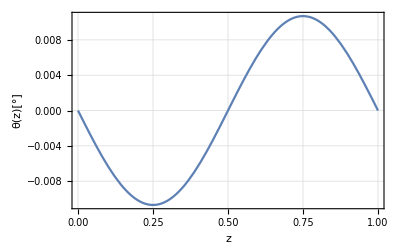
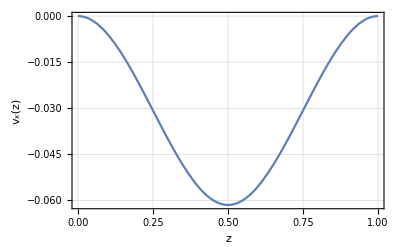
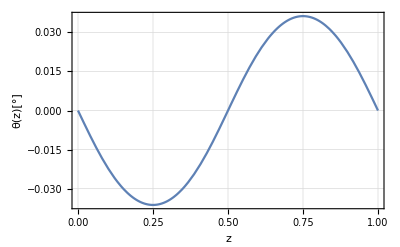
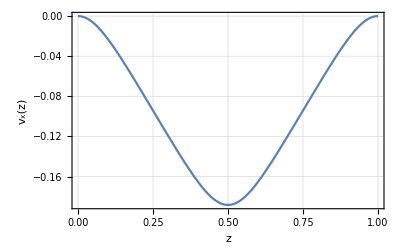
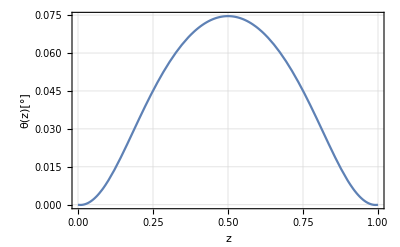
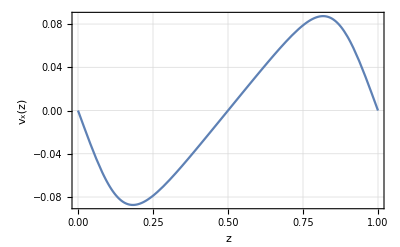
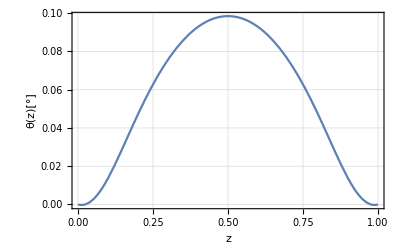
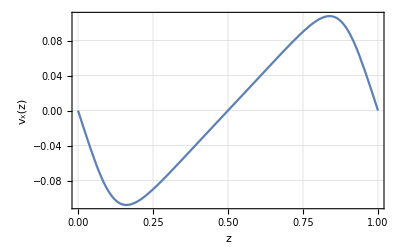
{{0.0201,-Graphics-,-Graphics-},{0.21,-Graphics-,-Graphics-},{0.44,-Graphics-,-Graphics-},{0.69,-Graphics-,-Graphics-},{0.8225,-Graphics-,-Graphics-},{0.96,-Graphics-,-Graphics-},{1.56,-Graphics-,-Graphics-},{2.24,-Graphics-,-Graphics-},{8,-Graphics-,-Graphics-},{35,-Graphics-,-Graphics-}}

```mathematica
"Solve Numerically without forcing"
Sol=Table[{val2=Join[val,{α->Al[[i]]}],Flatten[NDSolve[{(eq1//.val2)==0,(eq2//.val2)==0,q[0]==0,q[1]==0,V[0]==0,V[1]==0},{q,V},{ξ,0,1}]]},{i,1,Length[Al]}];

Table[{Al[[i]]^2-1,Plot[q[ξ]/.Sol[[i,2]],{ξ,0,1},Frame->True,FrameLabel->{"z","θ(z)[°]"},LabelStyle->Medium,GridLines->Automatic],
Plot[V[ξ]/.Sol[[i,2]],{ξ,0,1},Frame->True,FrameLabel->{"z","v_x(z)"},LabelStyle->Medium,GridLines->Automatic]},{i,1,Length[Al]}]
```

Forcing 1

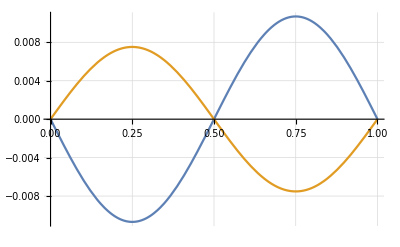
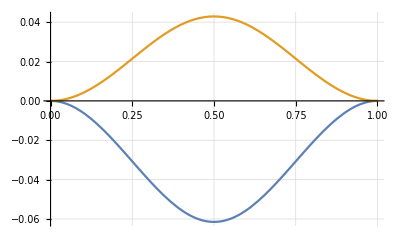
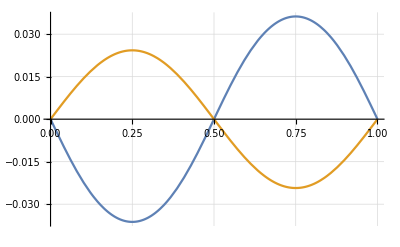
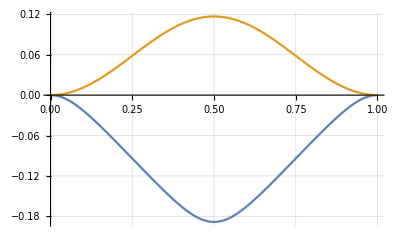
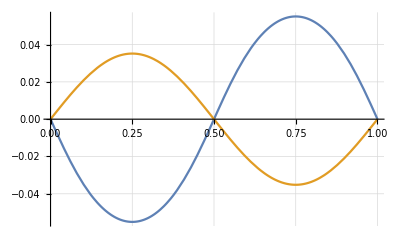
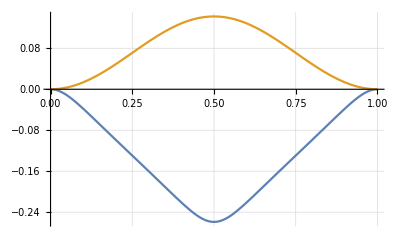
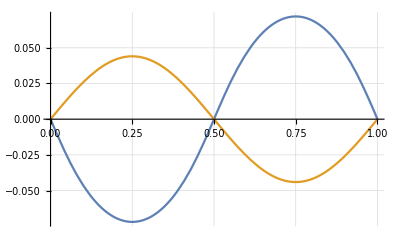
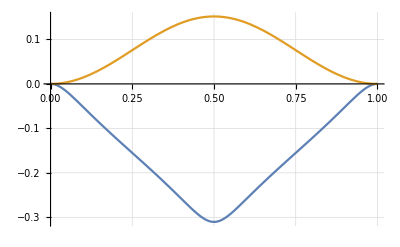
{{0.0201,-Graphics-,-Graphics-},{0.21,-Graphics-,-Graphics-},{0.44,-Graphics-,-Graphics-},{0.69,-Graphics-,-Graphics-},{0.8225,-Graphics-,-Graphics-},{0.96,-Graphics-,-Graphics-},{1.56,-Graphics-,-Graphics-},{2.24,-Graphics-,-Graphics-},{8,-Graphics-,-Graphics-},{35,-Graphics-,-Graphics-}}

```mathematica
"Forcing 1"
(*V[1/2] == (u1[1/2]//.val2), , q'[1/2] ==(θ1'[1/2]//.val2) ,V''[1/2] == (u1''[1/2]//.val2),q''[1/2] == (θ1''[1/2]//.val2)*)
Sol=Table[{val2=Join[val,{α->Al[[i]]}],Flatten[NDSolve[{(eq1//.val2)==0,(eq2//.val2)==0,q[0]==0,q[1]==0,V[0]==0,V[1]==0},{q[ξ],V[ξ]},{ξ,0,1},Method->"BoundaryValues"->{"Shooting", "StartingInitialConditions"->{ q[1/2] == (θ1[1/2]//.val2),V[1/2] == (u1[1/2]//.val2),V'[1/2] == (u1'[1/2]//.val2)}}]]},{i,1,Length[Al]}];

Table[{Al[[i]]^2-1,Plot[{q[ξ]/.Sol[[i,2]],θ1[ξ]/.{α->Al[[i]]}},{ξ,0,1},LabelStyle->Medium,GridLines->Automatic],
Plot[{V[ξ]/.Sol[[i,2]],u1[ξ]/.{α->Al[[i]]}},{ξ,0,1},GridLines->Automatic]},{i,1,Length[Al]}]
```

Forcig 2

FindRoot::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the function value is still greater than the tolerance prescribed by the AccuracyGoal option.

NDSolve::berr: The scaled boundary value residual error of 3.51759×10^7 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

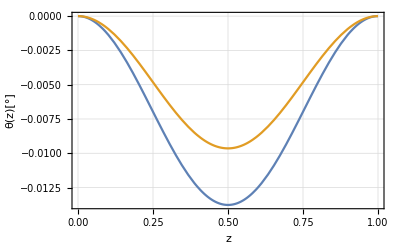
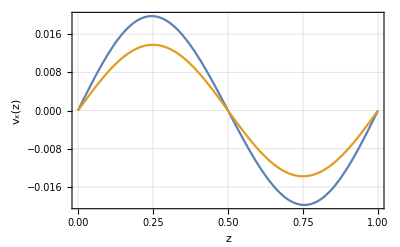
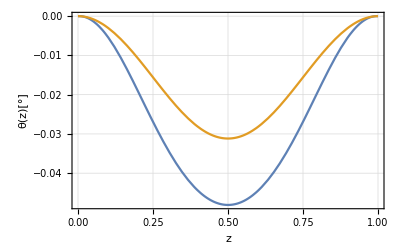
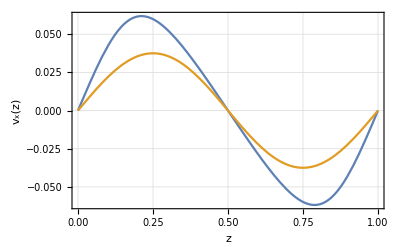
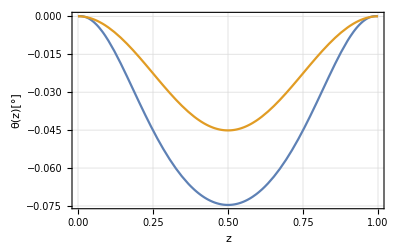
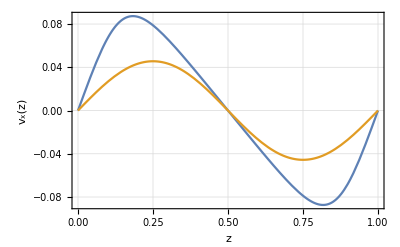
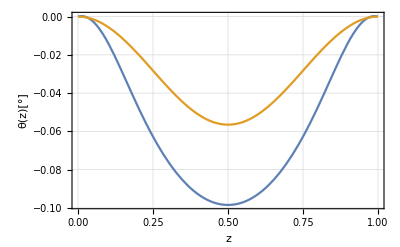
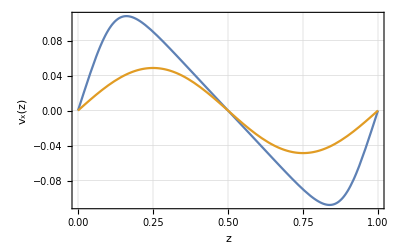
{{0.0201,-Graphics-,-Graphics-},{0.21,-Graphics-,-Graphics-},{0.44,-Graphics-,-Graphics-},{0.69,-Graphics-,-Graphics-},{0.8225,-Graphics-,-Graphics-},{0.96,-Graphics-,-Graphics-},{1.56,-Graphics-,-Graphics-},{2.24,-Graphics-,-Graphics-},{8,-Graphics-,-Graphics-},{35,-Graphics-,-Graphics-}}

```mathematica
"Forcig 2"
(*V[1/2] == (u2[1/2]//.val2), q[1/2] == (θ2[1/2]//.val2),V'[1/2] == (u2'[1/2]//.val2), q'[1/2] ==(θ2'[1/2]//.val2),V''[1/2] == (u2''[1/2]//.val2),q''[1/2] == (θ2''[1/2]//.val2)*)
Sol=Table[{val2=Join[val,{α->Al[[i]]}],Flatten[NDSolve[{(eq1//.val2)==0,(eq2//.val2)==0,q[0]==0,q[1]==0,V[0]==0,V[1]==0},{q,V},{ξ,0,1},Method->"BoundaryValues"->{"Shooting", "StartingInitialConditions"->{V[1/2] == (u2[1/2]//.val2), q[1/2] == (θ2[1/2]//.val2),V'[1/2] == (u2'[1/2]//.val2), q'[1/2] ==(θ2'[1/2]//.val2)}}]]},{i,1,Length[Al]}];

Table[{Al[[i]]^2-1,Plot[{q[ξ]/.Sol[[i,2]],θ2[ξ]/.{α->Al[[i]]}},{ξ,0,1},Frame->True,FrameLabel->{"z","θ(z)[°]"},LabelStyle->Medium,GridLines->Automatic],
Plot[{V[ξ]/.Sol[[i,2]],u2[ξ]/.{α->Al[[i]]}},{ξ,0,1},Frame->True,FrameLabel->{"z","v_x(z)"},LabelStyle->Medium,GridLines->Automatic]},{i,1,Length[Al]}]
```

## Numerical Solution (with dimension)

```mathematica
ClearAll["Global`*"]
val={a0->2.5,ζ->0.5,τ->1,L->1,μ->1,k->((a0^3-1)^2 L^2 ζ μ)/(4 a0 π^2 α^2)};  
r=μ L^2/k//.val;
λ=α^2-1;
r=μ L^2/k//.val;

(*Original equations*)

eq1=4 (-1+a0^3) (-2 a0 ζ Cos[2 q[ξ]]+2 τ (1+a0^3+(-1+a0^3) Cos[2 q[ξ]]) Sin[2 q[ξ]] V'[ξ]) q'[ξ]-τ (-5+2 a0^3-5 a0^6+4 (-1+a0^6) Cos[2 q[ξ]]+(-1+a0^3)^2 Cos[4 q[ξ]]) V''[ξ]/.val;
eq2=(-1+a0^3) μ τ (1-a0^3+(1+a0^3) Cos[2 q[ξ]]) V'[ξ]+2 a0^2 k q''[ξ]/.val;



(*Solutions of the Linear operator Kernel*)
bb=(a0^3-1)r/(2π a0^2)//.val;
al=4 a0^2 π √(α^2-1)/(r Sqrt[(6 a0^12-15 a0^9+17 a0^6-13 a0^3+5)])//.val
be =4 a0^2 π √(α^2-1)/(r Sqrt[(14 a0^12-27 a0^9+37 a0^6-49 a0^3+25)])//.val

u1[ξ_]=L/τ*al*(1-Cos[2 π ξ])//.val;
u2[ξ_]=L/τ*be*(Sin[2 π ξ])//.val;
θ1[ξ_]=al*(-1+a0^3) r/(2π a0^2)*(Sin[2 π ξ])//.val;
θ2[ξ_]=be*(-1+a0^3) r/(2π a0^2)*(Cos[2 π ξ]-1)//.val;

(*Alpha*)
Al={1.01,1.1,1.2,1.3,1.35,1.4,1.6,1.8,3,6};
```

(0.154262 √(-1+α^2))/α^2

(0.0989478 √(-1+α^2))/α^2

Solve Numerically without forcing

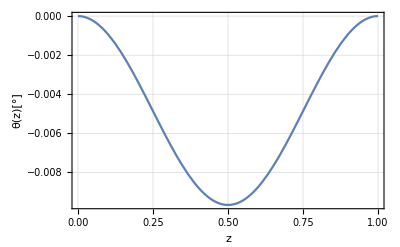
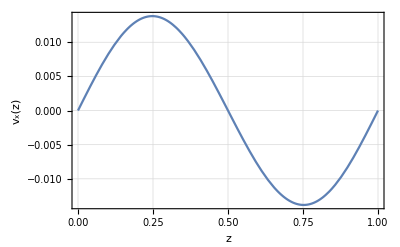
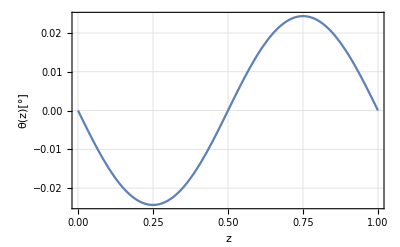
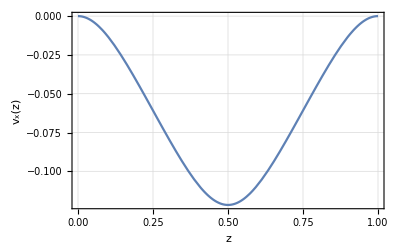
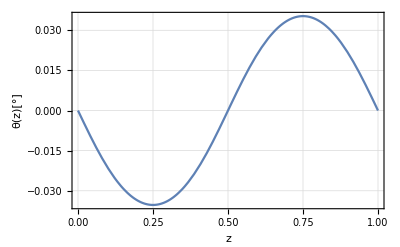
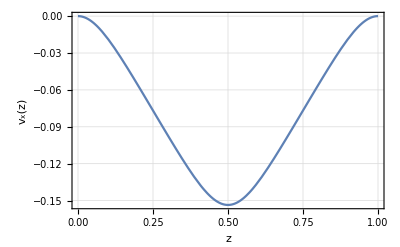
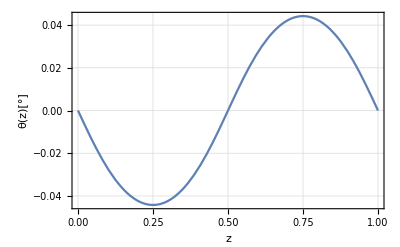
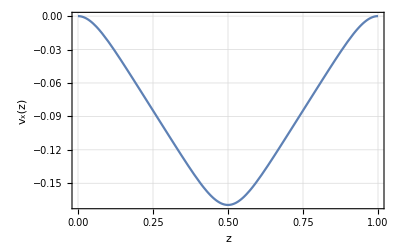
{{0.0201,-Graphics-,-Graphics-},{0.21,-Graphics-,-Graphics-},{0.44,-Graphics-,-Graphics-},{0.69,-Graphics-,-Graphics-},{0.8225,-Graphics-,-Graphics-},{0.96,-Graphics-,-Graphics-},{1.56,-Graphics-,-Graphics-},{2.24,-Graphics-,-Graphics-},{8,-Graphics-,-Graphics-},{35,-Graphics-,-Graphics-}}

```mathematica
"Solve Numerically without forcing"
Sol=Table[{val2=Join[val,{α->Al[[i]]}],Flatten[NDSolve[{(eq1//.val2)==0,(eq2//.val2)==0,q[0]==0,q[(L//.val2)]==0,V[0]==0,V[(L//.val2)]==0},{q[ξ],V[ξ]},{ξ,0,(L//.val2)}]]},{i,1,Length[Al]}];

Table[{Al[[i]]^2-1,Plot[q[ξ]/.Sol[[i,2]],{ξ,0,(L//.val2)},Frame->True,FrameLabel->{"z","θ(z)[°]"},LabelStyle->Medium,GridLines->Automatic],
Plot[V[ξ]/.Sol[[i,2]],{ξ,0,1},Frame->True,FrameLabel->{"z","v_x(z)"},LabelStyle->Medium,GridLines->Automatic]},{i,1,Length[Al]}]
```

```mathematica
"Forcing 1"
(*V[1/2] == (u1[1/2]//.val2), , q'[1/2] ==(θ1'[1/2]//.val2) ,V''[1/2] == (u1''[1/2]//.val2),q''[1/2] == (θ1''[1/2]//.val2)*)
Sol=Table[{val2=Join[val,{α->Al[[i]]}],Flatten[NDSolve[{(eq1//.val2)==0,(eq2//.val2)==0,q[0]==0,q[(L//.val2)]==0,V[0]==0,V[(L//.val2)]==0},{q[ξ],V[ξ]},{ξ,0,(L//.val2)},Method->"BoundaryValues"->{"Shooting", "StartingInitialConditions"->{ q[(L//.val2)/2] == (θ1[(L//.val2)/2]//.val2),V[(L//.val2)/2] == (u1[(L//.val2)/2]//.val2),V'[(L//.val2)/2] == (u1'[(L//.val2)/2]//.val2),V''[1/2] == (u1''[(L//.val2)/2]//.val2),q''[1/2] == (θ1''[(L//.val2)/2]//.val2)}}]]},{i,1,Length[Al]}];

Table[{Al[[i]]^2-1,Plot[{q[ξ]/.Sol[[i,2]],θ1[ξ]/.{α->Al[[i]]}},{ξ,0,(L//.val2)},LabelStyle->Medium,GridLines->Automatic],
Plot[{V[ξ]/.Sol[[i,2]],u1[ξ]/.{α->Al[[i]]}},{ξ,0,(L//.val2)},GridLines->Automatic]},{i,1,Length[Al]}]
```

Forcing 1

{{0.0201,-Graphics-,-Graphics-},{0.21,-Graphics-,-Graphics-},{0.44,-Graphics-,-Graphics-},{0.69,-Graphics-,-Graphics-},{0.8225,-Graphics-,-Graphics-},{0.96,-Graphics-,-Graphics-},{1.56,-Graphics-,-Graphics-},{2.24,-Graphics-,-Graphics-},{8,-Graphics-,-Graphics-},{35,-Graphics-,-Graphics-}}

Forcig 2

NDSolve::berr: The scaled boundary value residual error of 2.9751×10^7 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

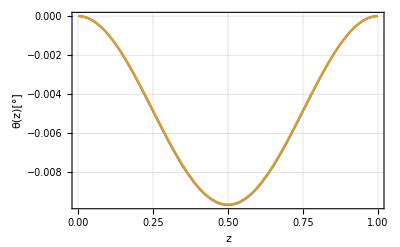
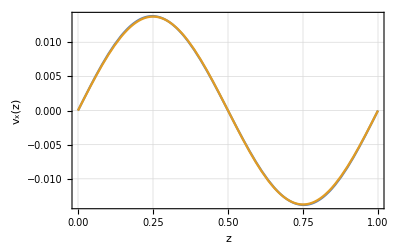
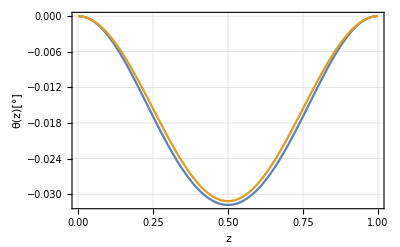
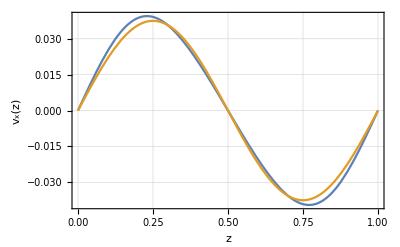
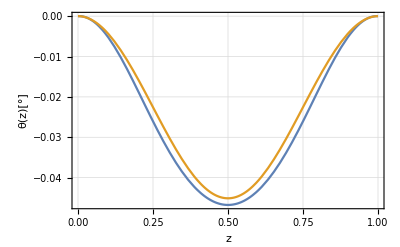
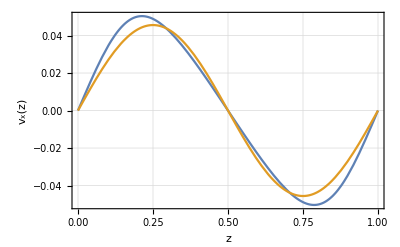
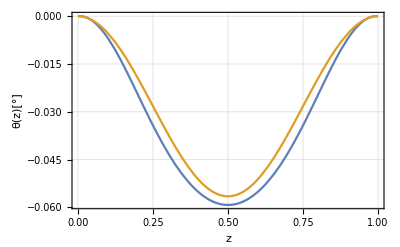
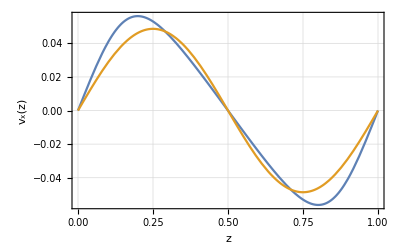
{{0.0201,-Graphics-,-Graphics-},{0.21,-Graphics-,-Graphics-},{0.44,-Graphics-,-Graphics-},{0.69,-Graphics-,-Graphics-},{0.8225,-Graphics-,-Graphics-},{0.96,-Graphics-,-Graphics-},{1.56,-Graphics-,-Graphics-},{2.24,-Graphics-,-Graphics-},{8,-Graphics-,-Graphics-},{35,-Graphics-,-Graphics-}}

```mathematica
"Forcing 2"
(*V[1/2] == (u2[1/2]//.val2), q[1/2] == (θ2[1/2]//.val2),V'[1/2] == (u2'[1/2]//.val2), q'[1/2] ==(θ2'[1/2]//.val2),V''[1/2] == (u2''[1/2]//.val2),q''[1/2] == (θ2''[1/2]//.val2)*)
Sol=Table[{val2=Join[val,{α->Al[[i]]}],Flatten[NDSolve[{(eq1//.val2)==0,(eq2//.val2)==0,q[0]==0,q[(L//.val2)]==0,V[0]==0,V[(L//.val2)]==0},{q[ξ],V[ξ]},{ξ,0,(L//.val2)},Method->"BoundaryValues"->{"Shooting", "StartingInitialConditions"->{V[(L//.val2)/2] == (u2[(L//.val2)/2]//.val2), q[(L//.val2)/2] == (θ2[(L//.val2)/2]//.val2),V'[(L//.val2)/2] == (u2'[(L//.val2)/2]//.val2), q'[1/2] ==(θ2'[(L//.val2)/2]//.val2)}}]]},{i,1,Length[Al]}];

Table[{Al[[i]]^2-1,Plot[{q[ξ]/.Sol[[i,2]],θ2[ξ]/.{α->Al[[i]]}},{ξ,0,(L//.val2)},Frame->True,FrameLabel->{"z","θ(z)[°]"},LabelStyle->Medium,GridLines->Automatic],
Plot[{V[ξ]/.Sol[[i,2]],u2[ξ]/.{α->Al[[i]]}},{ξ,0,(L//.val2)},Frame->True,FrameLabel->{"z","v_x(z)"},LabelStyle->Medium,GridLines->Automatic]},{i,1,Length[Al]}]
```